```mathematica
(* Example Mathematica notebook code for Figure 3 in main text *)
(* Run using Mathematica version 12.0.0.0 on Mac OS X x86 (64-bit) *)
```

```mathematica
(* define parameters *)

NN=20;
kk=5; 
m0=4;
mig=1;
 Nmig=750;

(* With migration, migration probability Pmigr *) Probmigr=0.1; (* Npatches patches, Moran process, size Ncells, X[i,t] mutants per patch at time t *) Npatches=1500; Ncells=NN; (* Initialize *) Do[X[i,0]=m0,{i,1,Npatches}]; (* Simulate birth death *)  Ntime=200;(* exchange Migset cells *)  Migset=kk; (* In each patch, the prob to get a mutant is p=X/Ncells. Prob to get m mutants is p^m*(1-p)^(Nmig-m) *) 

 cnt=0; Do[cnt=cnt+1; Do[X[i,t+1]=X[i,t];Pdivm=X[i,t]/Ncells; Pdiem=X[i,t]/Ncells; Pup=Pdivm*(1-Pdiem); Pdown=(1-Pdivm)*Pdiem; rr=Random[]; If[0<rr<Pup, X[i,t+1]=X[i,t+1]+1,If[Pup<rr<Pup+Pdown,X[i,t+1]=X[i,t+1]-1]],{i,1,Npatches}]; (* Now perform migration Npatches/2 times *) 

If[cnt==mig, {cnt=0; Do[i1=RandomInteger[{1,Npatches}];
 mut1=RandomVariate[HypergeometricDistribution[Migset,X[i1,t+1],Ncells]];i2=RandomInteger[{1,Npatches}];mut2=RandomVariate[HypergeometricDistribution[Migset,X[i2,t+1],Ncells]]; mut1=Min[{mut1, X[i1,t+1]}];mut2=Min[{mut2, X[i2,t+1]}];dif=mut1-mut2; X[i1,t+1]=X[i1,t+1]-dif; X[i2,t+1]=X[i2,t+1]+dif,{jj,1,Nmig}]}],{t,0,Ntime}];

(* No migration *) (* Npatches patches, Moran process, size Ncells, X[i,t] mutants per patch at time t *) Npatches=1500; Ncells=NN; (*Initialize *) Do[Xnom[i,0]=m0,{i,1,Npatches}]; (* Simulate birth death *) Ntime=200;(* exchange Migset cells *) Migset=kk; (* In each patch, the prob to get a mutant is p=X/Ncells. Prob to get m mutants is p^m*(1-p)^(Nmig-m) *) 

 cnt=0; Do[cnt=cnt+1; Do[Xnom[i,t+1]=Xnom[i,t];Pdivm=Xnom[i,t]/Ncells; Pdiem=Xnom[i,t]/Ncells; Pup=Pdivm*(1-Pdiem); Pdown=(1-Pdivm)*Pdiem; rr=Random[]; If[0<rr<Pup, Xnom[i,t+1]=Xnom[i,t+1]+1,If[Pup<rr<Pup+Pdown,Xnom[i,t+1]=Xnom[i,t+1]-1]],{i,1,Npatches}]; ,{t,0,Ntime}];

Nsteps = 150;
Do[Do[a[i,j]=0,{i,0,NN}],{j,0,NN}];a[0,0]=1; a[NN,NN]=1;
Do[a[i,i]=1-2*i/NN*(1-i/NN); a[i,i+1]=i/NN*(1-i/NN); a[i,i-1]=i/NN*(1-i/NN),{i,1,NN-1}]; Ptrans=Table[a[i,j],{i,0,NN},{j,0,NN}];

 m=.; n=.; Do[Do[rho[i,j]=0,{i,0,NN}],{j,-NN,2*NN}];Do[Do[rho[m,n]=Binomial[kk,n]*Binomial[NN-kk,m-n]/Binomial[NN,m],{n,0,kk}],{m,0,NN}]

Pmigr=.;
Probmigr=0;pinom[0]=Table[If[m==m0,1,0],{m,0,NN}];Do[Do[Do[(* calculate the probability to go from m1 mutants to m2 mutants *) prob[m1,m2]=Probmigr* Sum[rho[m1,n1]*Sum[pinom[t-1][[mm+1]]*rho[mm,m2-m1+n1],{mm,0,NN}],{n1,0,kk}]+(1-Probmigr)*KroneckerDelta[m1,m2],{m1,0,NN}],{m2,0,NN}]; Pmigr=Table[prob[m1,m2],{m1,0,NN},{m2,0,NN}]; pinom[t]=pinom[t-1].Pmigr.Ptrans,{t,1,Nsteps}]

Pmigr=.;
Probmigr=1;pi[0]=Table[If[m==m0,1,0],{m,0,NN}];Do[Do[Do[(* calculate the probability to go from m1 mutants to m2 mutants *) prob[m1,m2]=Probmigr* Sum[rho[m1,n1]*Sum[pi[t-1][[mm+1]]*rho[mm,m2-m1+n1],{mm,0,NN}],{n1,0,kk}]+(1-Probmigr)*KroneckerDelta[m1,m2],{m1,0,NN}],{m2,0,NN}]; Pmigr=Table[prob[m1,m2],{m1,0,NN},{m2,0,NN}]; pi[t]=pi[t-1].Pmigr.Ptrans,{t,1,Nsteps}]
```

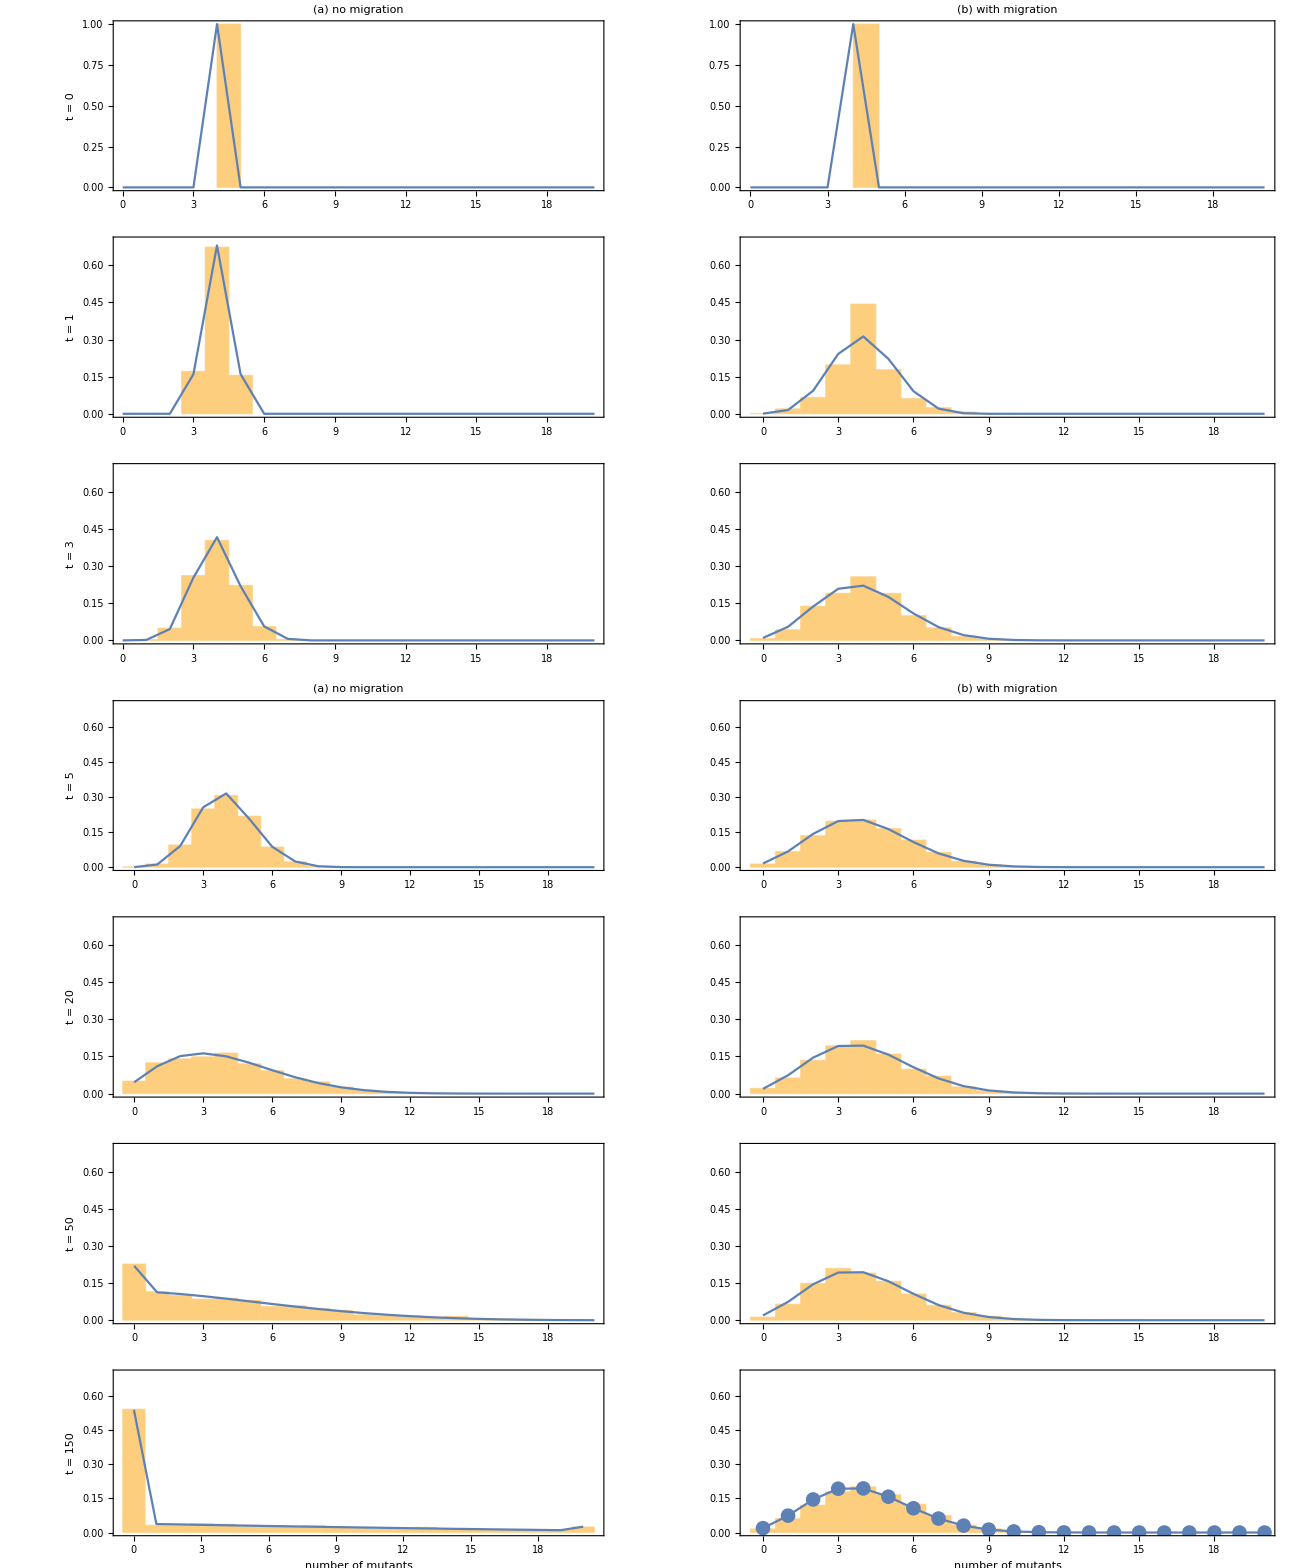

```mathematica
(* plot *)

(* Make a table of several examples with different time *) t1=0; t2=121; tsh=5; Do[Time=t1+it*tsh; Xfnom[it]=Table[Xnom[i,Ti[it]],{i,1,Npatches}],{it,0,6}]

(* Make a table of several examples with different time *) t1=0; t2=121; tsh=1;Ti[0]=0; Ti[1]=1; Ti[2]=3; Ti[3]=5; Ti[4]=20; Ti[5]=50; Ti[6]=150; Do[Time=t1+it*tsh; Xf[it]=Table[X[i,Ti[it]],{i,1,Npatches}],{it,0,6}]

TableForm[Table[Show[Histogram[Xfnom[it],{1},"PDF"],ListPlot[Table[{k-1,pinom[Ti[it]][[k]]},{k,1,Length[pi[1]]}],PlotRange->All,Joined->True],PlotRange->{0,0.7},Frame->True,BaseStyle->Medium],{it,0,6}]];

TableForm[Table[Show[Histogram[Xf[it],{1},"PDF"],ListPlot[Table[{k-1,pi[Ti[it]][[k]]},{k,1,Length[pi[1]]}],PlotRange->All,Joined->True],PlotRange->{0,0.7},Frame->True,BaseStyle->Medium],{it,0,6}]];

N1 =Show[Histogram[Xfnom[0],{1},"PDF"],ListPlot[Table[{k-1,pinom[Ti[0]][[k]]},{k,1,Length[pi[1]]}],PlotRange->All,Joined->True],PlotRange->{0,1},Frame->True,BaseStyle->Medium,ImageSize->{600,600},FrameStyle->Bold,PlotLabel->"(a) no migration",AspectRatio-> Full,LabelStyle->{Bold,FontSize->36, FontColor->Black},FrameLabel->{"","t = 0"}];
N2 = Show[Histogram[Xfnom[1],{1},"PDF"],ListPlot[Table[{k-1,pinom[Ti[1]][[k]]},{k,1,Length[pi[1]]}],PlotRange->All,Joined->True],PlotRange->{0,0.7},Frame->True,BaseStyle->Medium,ImageSize->{600,600},FrameStyle->Bold,AspectRatio-> Full,LabelStyle->{Bold,FontSize->36, FontColor->Black},FrameLabel->{"","t = 1"}];
N3 = Show[Histogram[Xfnom[2],{1},"PDF"],ListPlot[Table[{k-1,pinom[Ti[2]][[k]]},{k,1,Length[pi[1]]}],PlotRange->All,Joined->True],PlotRange->{0,0.7},Frame->True,BaseStyle->Medium,ImageSize->{600,600},FrameStyle->Bold,AspectRatio-> Full,LabelStyle->{Bold,FontSize->36, FontColor->Black},FrameLabel->{"","t = 3"}];
N4 = Show[Histogram[Xfnom[3],{1},"PDF"],ListPlot[Table[{k-1,pinom[Ti[3]][[k]]},{k,1,Length[pi[1]]}],PlotRange->All,Joined->True],PlotRange->{0,0.7},Frame->True,BaseStyle->Medium,ImageSize->{600,600},FrameStyle->Bold,AspectRatio-> Full,LabelStyle->{Bold,FontSize->36, FontColor->Black},FrameLabel->{"","t = 5"},PlotLabel->"(a) no migration"];
N5 = Show[Histogram[Xfnom[4],{1},"PDF"],ListPlot[Table[{k-1,pinom[Ti[4]][[k]]},{k,1,Length[pi[1]]}],PlotRange->All,Joined->True],PlotRange->{0,0.7},Frame->True,BaseStyle->Medium,ImageSize->{600,600},FrameStyle->Bold,AspectRatio-> Full,LabelStyle->{Bold,FontSize->36, FontColor->Black},FrameLabel->{"","t = 20"}];
N6 = Show[Histogram[Xfnom[5],{1},"PDF"],ListPlot[Table[{k-1,pinom[Ti[5]][[k]]},{k,1,Length[pi[1]]}],PlotRange->All,Joined->True],PlotRange->{0,0.7},Frame->True,BaseStyle->Medium,ImageSize->{600,600},FrameStyle->Bold,AspectRatio-> Full,LabelStyle->{Bold,FontSize->36, FontColor->Black},FrameLabel->{"","t = 50"}];
N7 = Show[Histogram[Xfnom[6],{1},"PDF"],ListPlot[Table[{k-1,pinom[Ti[6]][[k]]},{k,1,Length[pi[1]]}],PlotRange->All,Joined->True],PlotRange->{0,0.7},Frame->True,BaseStyle->Medium, ImageSize->{600,600},FrameStyle->Bold,AspectRatio-> Full,LabelStyle->{Bold,FontSize->36, FontColor->Black},FrameLabel->{"number of mutants","t = 150"}];

W1 = Show[Histogram[Xf[0],{1},"PDF"],ListPlot[Table[{k-1,pi[Ti[0]][[k]]},{k,1,Length[pi[1]]}],PlotRange->All,Joined->True],PlotRange->{0,1},Frame->True,BaseStyle->Medium,ImageSize->{600,600},FrameStyle->Bold,AspectRatio-> Full,LabelStyle->{Bold,FontSize->36, FontColor->Black},PlotLabel->"(b) with migration"];
W2 = Show[Histogram[Xf[1],{1},"PDF"],ListPlot[Table[{k-1,pi[Ti[1]][[k]]},{k,1,Length[pi[1]]}],PlotRange->All,Joined->True],PlotRange->{0,0.7},Frame->True,BaseStyle->Medium,ImageSize->{600,600},FrameStyle->Bold,AspectRatio-> Full,LabelStyle->{Bold,FontSize->36, FontColor->Black}];
W3 = Show[Histogram[Xf[2],{1},"PDF"],ListPlot[Table[{k-1,pi[Ti[2]][[k]]},{k,1,Length[pi[1]]}],PlotRange->All,Joined->True],PlotRange->{0,0.7},Frame->True,BaseStyle->Medium,ImageSize->{600,600},FrameStyle->Bold,AspectRatio-> Full,LabelStyle->{Bold,FontSize->36, FontColor->Black}];
W4 = Show[Histogram[Xf[3],{1},"PDF"],ListPlot[Table[{k-1,pi[Ti[3]][[k]]},{k,1,Length[pi[1]]}],PlotRange->All,Joined->True],PlotRange->{0,0.7},Frame->True,BaseStyle->Medium,ImageSize->{600,600},FrameStyle->Bold,AspectRatio-> Full,LabelStyle->{Bold,FontSize->36, FontColor->Black},PlotLabel->"(b) with migration"];
W5 = Show[Histogram[Xf[4],{1},"PDF"],ListPlot[Table[{k-1,pi[Ti[4]][[k]]},{k,1,Length[pi[1]]}],PlotRange->All,Joined->True],PlotRange->{0,0.7},Frame->True,BaseStyle->Medium,ImageSize->{600,600},FrameStyle->Bold,AspectRatio-> Full,LabelStyle->{Bold,FontSize->36, FontColor->Black}];
W6 = Show[Histogram[Xf[5],{1},"PDF"],ListPlot[Table[{k-1,pi[Ti[5]][[k]]},{k,1,Length[pi[1]]}],PlotRange->All,Joined->True],PlotRange->{0,0.7},Frame->True,BaseStyle->Medium,ImageSize->{600,600},FrameStyle->Bold,AspectRatio-> Full,LabelStyle->{Bold,FontSize->36, FontColor->Black}];
W7 = Show[Histogram[Xf[6],{1},"PDF"],ListPlot[Table[{k-1,pi[Ti[6]][[k]]},{k,1,Length[pi[1]]}],PlotRange->All,PlotMarkers->{Automatic,15},Joined->True],PlotRange->{0,0.7},Frame->True,BaseStyle->Medium,ImageSize->{600,600},FrameStyle->Bold,AspectRatio-> Full,LabelStyle->{Bold,FontSize->36, FontColor->Black},FrameLabel->{"number of mutants",""}];

GraphicsGrid[{{N1,W1},{N2,W2},{N3,W3},{N4,W4},{N5,W5},{N6,W6},{N7,W7}},ImageSize->{1300,500*7},AspectRatio->Full]
GraphicsGrid[{{N4,W4},{N5,W5},{N6,W6},{N7,W7}},ImageSize->{1300,500*5},AspectRatio->Full];
```